```mathematica
ClearAll["Global`*"]
```

```mathematica
ac=0.4;
```

```mathematica
pai=Table[1-(i-1)(1-ac)/30,{i,1,31}];
```

```mathematica
pai
```

{1.,0.98,0.96,0.94,0.92,0.9,0.88,0.86,0.84,0.82,0.8,0.78,0.76,0.74,0.72,0.7,0.68,0.66,0.64,0.62,0.6,0.58,0.56,0.54,0.52,0.5,0.48,0.46,0.44,0.42,0.4}

```mathematica
pzi=1/pai-1
```

{0.,0.0204082,0.0416667,0.0638298,0.0869565,0.111111,0.136364,0.162791,0.190476,0.219512,0.25,0.282051,0.315789,0.351351,0.388889,0.428571,0.470588,0.515152,0.5625,0.612903,0.666667,0.724138,0.785714,0.851852,0.923077,1.,1.08333,1.17391,1.27273,1.38095,1.5}

```mathematica
threeqz04=Import["D:\\1work\\rec-qz\\data-3-result\\qz-0.4.txt","Table"]
```

{{q0,-0.731386,0.187778},{q1,-0.653929,0.139453},{q2,-0.584813,0.0990842},{q3,-0.523417,0.067198},{q4,-0.469122,0.0456751},{q5,-0.421312,0.0376907},{q6,-0.379376,0.0412691},{q7,-0.342707,0.0486136},{q8,-0.310706,0.0550525},{q9,-0.282777,0.0591178},{q10,-0.258336,0.0605602},{q11,-0.236805,0.0595808},{q12,-0.217617,0.0565966},{q13,-0.200214,0.0521842},{q14,-0.184051,0.0471007},{q15,-0.168595,0.0423383},{q16,-0.153324,0.0391117},{q17,-0.137732,0.0385368},{q18,-0.121323,0.040962},{q19,-0.103617,0.0457067},{q20,-0.0841441,0.0516005},{q21,-0.0624468,0.0575351},{q22,-0.0380776,0.0626166},{q23,-0.0105971,0.0661248},{q24,0.0204285,0.0674499},{q25,0.0554294,0.0660477},{q26,0.0948358,0.0614145},{q27,0.139081,0.0530738},{q28,0.188605,0.0405753},{q29,0.243858,0.0235449},{q30,0.305302,0.00439948}}

```mathematica
threeqz04={{"q0",-0.731386,0.187778},{"q1",-0.653929,0.139453},{"q2",-0.584813,0.0990842},{"q3",-0.523417,0.067198},{"q4",-0.469122,0.0456751},{"q5",-0.421312,0.0376907},{"q6",-0.379376,0.0412691},{"q7",-0.342707,0.0486136},{"q8",-0.310706,0.0550525},{"q9",-0.282777,0.0591178},{"q10",-0.258336,0.0605602},{"q11",-0.236805,0.0595808},{"q12",-0.217617,0.0565966},{"q13",-0.200214,0.0521842},{"q14",-0.184051,0.0471007},{"q15",-0.168595,0.0423383},{"q16",-0.153324,0.0391117},{"q17",-0.137732,0.0385368},{"q18",-0.121323,0.040962},{"q19",-0.103617,0.0457067},{"q20",-0.0841441,0.0516005},{"q21",-0.0624468,0.0575351},{"q22",-0.0380776,0.0626166},{"q23",-0.0105971,0.0661248},{"q24",0.0204285,0.0674499},{"q25",0.0554294,0.0660477},{"q26",0.0948358,0.0614145},{"q27",0.139081,0.0530738},{"q28",0.188605,0.0405753},{"q29",0.243858,0.0235449},{"q30",0.305302,0.00439948}};
```

```mathematica
threeqz=Table[{0,0,0},31]
```

{{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0}}

```mathematica
Do[threeqz[[i]][[1]]=pzi[[i]];threeqz[[i]][[2]]=threeqz04[[i]][[2]];threeqz[[i]][[3]]=threeqz04[[i]][[3]];,{i,1,31}]
```

```mathematica
threeqz
```

{{0.,-0.731386,0.187778},{0.0204082,-0.653929,0.139453},{0.0416667,-0.584813,0.0990842},{0.0638298,-0.523417,0.067198},{0.0869565,-0.469122,0.0456751},{0.111111,-0.421312,0.0376907},{0.136364,-0.379376,0.0412691},{0.162791,-0.342707,0.0486136},{0.190476,-0.310706,0.0550525},{0.219512,-0.282777,0.0591178},{0.25,-0.258336,0.0605602},{0.282051,-0.236805,0.0595808},{0.315789,-0.217617,0.0565966},{0.351351,-0.200214,0.0521842},{0.388889,-0.184051,0.0471007},{0.428571,-0.168595,0.0423383},{0.470588,-0.153324,0.0391117},{0.515152,-0.137732,0.0385368},{0.5625,-0.121323,0.040962},{0.612903,-0.103617,0.0457067},{0.666667,-0.0841441,0.0516005},{0.724138,-0.0624468,0.0575351},{0.785714,-0.0380776,0.0626166},{0.851852,-0.0105971,0.0661248},{0.923077,0.0204285,0.0674499},{1.,0.0554294,0.0660477},{1.08333,0.0948358,0.0614145},{1.17391,0.139081,0.0530738},{1.27273,0.188605,0.0405753},{1.38095,0.243858,0.0235449},{1.5,0.305302,0.00439948}}

```mathematica
line1=Table[threeqz[[i,{1,2}]],{i,Length[threeqz]}];
line3=Table[{threeqz[[i,1]],threeqz[[i,2]]-threeqz[[i,3]]/2},{i,Length[threeqz]}];
line2=Table[{threeqz[[i,1]],threeqz[[i,2]]+threeqz[[i,3]]/2},{i,Length[threeqz]}];
```

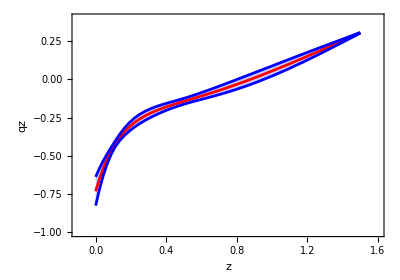

```mathematica
ListLinePlot[{line1,line2,line3},PlotRange->{{-0.1,1.6},{-1,0.4}},PlotStyle->{Red,Blue,Blue},Frame->True,FrameStyle->Directive[Black,Bold],FrameTicksStyle->{Black,Bold},LabelStyle->Directive[16,Bold],AspectRatio->0.7,FrameLabel->{"z","qz"},LabelStyle->Directive[12,Bold],Filling->{2->{3}}]
```